```mathematica
<<DimerSystem`
```

```mathematica
?DimerSystem
```

Dimer System V-0.3, 02/02/2017

Contributed by authors in ArXiv:..

This is a computational package of bipartite field theory. Given any theory with the SL(2,ℤ) reduced 2-d toric diagram, the package is able to compute its corresponding dimer model, super-potential terms and quiver graph. 

The package is brounght in along with the paper: XXXXXXXX TO BE FILLED IN XXXXXXX

The DimerSystem contains the following modules:
________________________
1) RecDimerModels[]
2) ToricInfo[]
3) DrawPerfectMatching[]
4) TriangDimer[]
5) RemovePointsParallel[]
6) HiggsingDimerSU[]
________________________
Use ?NameOfModule to view the details of each module.
Use DimerDemo[] to view a demonstration of dP3 surface.

```mathematica
?RecDimerModels
```

Initialise the rectangular dimer model.
________________________
RecDimerModels[m,n] will returns the initialised dimer model 
as the Z_m x Z_n quotient of a conifold. 
The output is in the form 
{DimerGraph -> # graph representation of the m x n dimer model #, KMatrix-> # the Kasteleyn matrix #}.

```mathematica
?ToricInfo
```

Compute the perfect matchings and toric diagram given a Kasteleyn matrix.
________________________
ToricInfo[KM,_QPrintFormat] will output the following list:
{KMatrix -> # the K matrix (same as input) #, PMatrix -> # the perfect matchings in a matrix form, where 1 stands for the presence of a field in a perfect matching. #, PerfectMatchings -> # a readable form of perfect matchings, denoting all the fields X_{i,j} #, ToricDiagram -> # the toric digram #, ToricPerfMap -> # denoting the correspondence between toric points and perfect matchings. #, FieldsPerfInfo -> # the counting of which perfect matchings contain a certain field #, ToricPts -> # the list of toric points. #}
If the user set the default parameter QPrintFormat as True, then the module will firstly print out a readable form of all the above items.

```mathematica
?DrawPerfectMatching
```

Highlight a perfect matching in the brane tiling.
________________________
DrawPerfectMatching[APerfectMatching] will ouput a graphical representation of the input perfect matching, highlighted in dotted green lines.

```mathematica
?TriangDimer
```

Triangulation of a dimer model, with some fields deleted.
________________________
TriangDimer[KM,# fields to remove #] will output the triangulated toric diagram, if certain fields were removed from a dimer with Kasteleyn matrix KM.

```mathematica
?RemovePointsParallel
```

Compute the partial resolutions given the Kasteleyn matrix and points to remove.
________________________
RemovePointsParallel[KM, # points to remove from a toric diagram #] will start all kernels and compute all the possible partial resolutions if we want to remove certain points from a dimer model with Kasteleyn matrix KM.

```mathematica
?HiggsingDimerSU
```

Compute the dimer model of the target geometry.
________________________
HiggsingDimerSU[# fields to remove #] will output the following result: {HiggsingDimer -> # graphical object representing the new dimer model #, SUW -> # the super-potential terms of the new dimer model #, Quiver -> # the new quiver graph #, Content -> # summary of all field contents #}

This is a simple demonstration of computing dP3 geometry.

Input:

RecDimerModels[2,2]

Output:

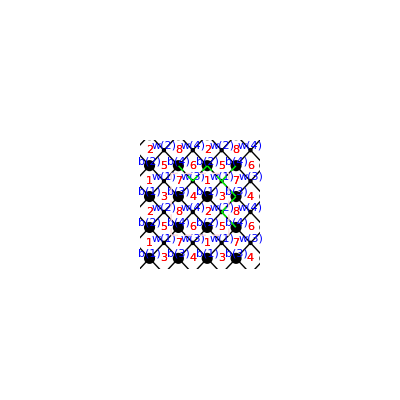
{DimerGraph→-Graphics-,KMatrix→{{X_{1,3},X_{3,2},X_{4,1},X_{2,4}},{y X_{5,1},X_{2,5},y X_{1,6},X_{6,2}},{x X_{3,7},x X_{8,3},X_{7,4},X_{4,8}},{x y X_{7,5},x X_{5,8},y X_{6,7},X_{8,6}}}}

Now that we know the K matrix, we can use ToricInfo[] to compute the perfect matchings.

Input:

ToricInfo[{{X_{1, 3},X_{3, 2},X_{4, 1},X_{2, 4}},{y X_{5, 1},X_{2, 5},y X_{1, 6},X_{6, 2}},{x X_{3, 7},x X_{8, 3},X_{7, 4},X_{4, 8}},{x y X_{7, 5},x X_{5, 8},y X_{6, 7},X_{8, 6}}}]

Output:

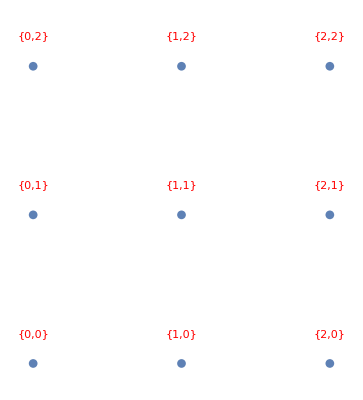
{KMatrix→{{X_{1,3},X_{3,2},X_{4,1},X_{2,4}},{y X_{5,1},X_{2,5},y X_{1,6},X_{6,2}},{x X_{3,7},x X_{8,3},X_{7,4},X_{4,8}},{x y X_{7,5},x X_{5,8},y X_{6,7},X_{8,6}}},PMatrix→{{0,0,0,0,0,0,0,1,1,0,1,0,1,0,0,0,0,0,0,0,1,0,1,0},{0,0,1,1,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0},{0,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,1,0,0,0,1,0,0,1,1,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,1,0,0},{1,0,0,0,0,1,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,1,0,0},{1,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,1},{0,1,0,1,0,0,0,0,0,0,1,0,1,1,0,0,0,1,0,0,0,0,0,0},{0,1,0,0,1,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,1},{1,0,0,0,0,1,0,0,1,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0},{0,1,0,0,1,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,1,0,1,1,0,0,0,0},{0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0},{0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1},{0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,1,1,1}},PerfectMatchings→{X_{3,7} X_{4,1} X_{5,8} X_{6,2},X_{3,2} X_{4,8} X_{5,1} X_{6,7},X_{1,6} X_{2,4} X_{7,5} X_{8,3},X_{1,6} X_{3,2} X_{4,8} X_{7,5},X_{2,4} X_{5,1} X_{6,7} X_{8,3},X_{1,6} X_{2,4} X_{3,7} X_{5,8},X_{4,1} X_{6,2} X_{7,5} X_{8,3},X_{1,3} X_{2,5} X_{7,4} X_{8,6},X_{1,3} X_{5,8} X_{6,2} X_{7,4},X_{2,5} X_{3,7} X_{4,1} X_{8,6},X_{1,3} X_{2,5} X_{4,8} X_{6,7},X_{3,2} X_{5,1} X_{7,4} X_{8,6},X_{1,3} X_{1,6} X_{4,8} X_{5,8},X_{4,1} X_{4,8} X_{5,1} X_{5,8},X_{2,4} X_{2,5} X_{3,7} X_{6,7},X_{3,2} X_{3,7} X_{6,2} X_{6,7},X_{2,4} X_{5,1} X_{5,8} X_{7,4},X_{2,5} X_{4,1} X_{4,8} X_{7,5},X_{2,4} X_{2,5} X_{7,4} X_{7,5},X_{3,2} X_{6,2} X_{7,4} X_{7,5},X_{1,3} X_{6,2} X_{6,7} X_{8,3},X_{1,6} X_{3,2} X_{3,7} X_{8,6},X_{1,3} X_{1,6} X_{8,3} X_{8,6},X_{4,1} X_{5,1} X_{8,3} X_{8,6}},ToricDiagram→-Graphics-,ToricPerfMap→{{2,2}→p[3],{2,1}→-p[6]-p[7],{2,0}→p[1],{1,2}→-p[4]-p[5],{1,1}→p[13]-p[14]+p[15]-p[16]+p[17]+p[18]-p[19]+p[20]+p[21]+p[22]-p[23]+p[24],{1,0}→-p[9]-p[10],{0,2}→p[2],{0,1}→-p[11]-p[12],{0,0}→p[8]},FieldsPerfInfo→{X_{1,3}→{p[8],p[9],p[11],p[13],p[21],p[23]},X_{1,6}→{p[3],p[4],p[6],p[13],p[22],p[23]},X_{2,4}→{p[3],p[5],p[6],p[15],p[17],p[19]},X_{2,5}→{p[8],p[10],p[11],p[15],p[18],p[19]},X_{3,2}→{p[2],p[4],p[12],p[16],p[20],p[22]},X_{3,7}→{p[1],p[6],p[10],p[15],p[16],p[22]},X_{4,1}→{p[1],p[7],p[10],p[14],p[18],p[24]},X_{4,8}→{p[2],p[4],p[11],p[13],p[14],p[18]},X_{5,1}→{p[2],p[5],p[12],p[14],p[17],p[24]},X_{5,8}→{p[1],p[6],p[9],p[13],p[14],p[17]},X_{6,2}→{p[1],p[7],p[9],p[16],p[20],p[21]},X_{6,7}→{p[2],p[5],p[11],p[15],p[16],p[21]},X_{7,4}→{p[8],p[9],p[12],p[17],p[19],p[20]},X_{7,5}→{p[3],p[4],p[7],p[18],p[19],p[20]},X_{8,3}→{p[3],p[5],p[7],p[21],p[23],p[24]},X_{8,6}→{p[8],p[10],p[12],p[22],p[23],p[24]}},ToricPts→{{2,2},{2,1},{2,0},{1,2},{1,1},{1,0},{0,2},{0,1},{0,0}}}

One can view a certain perfect matching using DrawPerfectMatching[].

Input:

DrawPerfectMatching[X_{4, 1} X_{5, 1} X_{8, 3} X_{8, 6}]

Output:

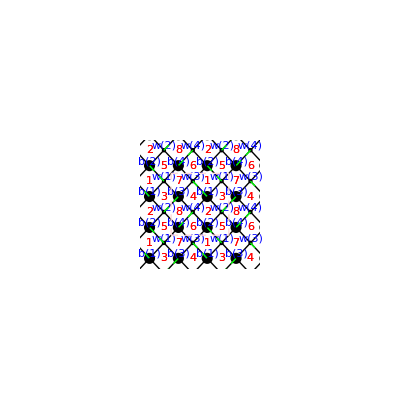

Next, we want to compute the higgsing of dP3 toric diagram, and we need to remove the points {0,2} and {2,0} from the original toric diagram.

Input:

RemovePointsParallel[{{X_{1, 3},X_{3, 2},X_{4, 1},X_{2, 4}},{y X_{5, 1},X_{2, 5},y X_{1, 6},X_{6, 2}},{x X_{3, 7},x X_{8, 3},X_{7, 4},X_{4, 8}},{x y X_{7, 5},x X_{5, 8},y X_{6, 7},X_{8, 6}}},{{0,2},{2,0}}]

Output:

2 of 8 ,temp Length = 16 No. of fields in each choice = 2 ,Length of wronglist = 12

3 of 8 ,temp Length = 0 No. of fields in each choice = 3 ,Length of wronglist = 23

4 of 8 ,temp Length = 0 No. of fields in each choice = 4 ,Length of wronglist = 23

5 of 8 ,temp Length = 0 No. of fields in each choice = 5 ,Length of wronglist = 23

6 of 8 ,temp Length = 0 No. of fields in each choice = 6 ,Length of wronglist = 23

7 of 8 ,temp Length = 0 No. of fields in each choice = 7 ,Length of wronglist = 23

8 of 8 ,temp Length = 0 No. of fields in each choice = 8 ,Length of wronglist = 23

{1.51328,{{X_{3,7},X_{6,7}},{X_{4,1},X_{4,8}},{X_{4,1},X_{5,1}},{X_{4,1},X_{6,7}},{X_{4,8},X_{5,8}},{X_{4,8},X_{6,2}},{X_{5,1},X_{5,8}},{X_{5,1},X_{6,2}},{X_{5,8},X_{6,7}},{X_{6,2},X_{6,7}}}}

Choosing one of the higgsing plan, we can compute the quiver graph, super-potential terms and field contents using HiggsingDimerSU[].

Input:

HiggsingDimerSU[{X_{4, 8},X_{6, 2}}]

Output:

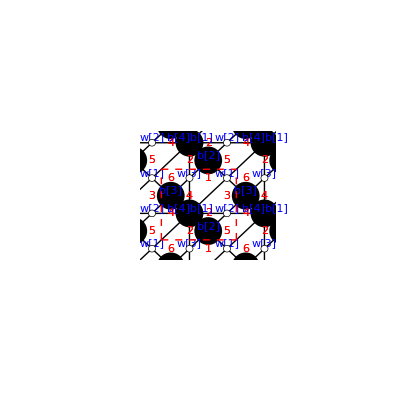
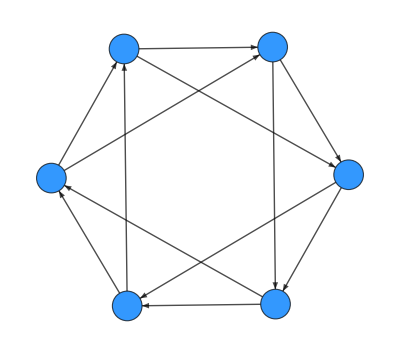
{HiggsingDimer→-Graphics-,SUW→{-X_{1,3} X_{2,6} X_{3,2} X_{4,1} X_{5,4} X_{6,5},-X_{1,2} X_{2,5} X_{5,1},-X_{3,6} X_{4,3} X_{6,4},X_{1,3} X_{3,6} X_{5,1} X_{6,5},X_{2,5} X_{3,2} X_{4,3} X_{5,4},X_{1,2} X_{2,6} X_{4,1} X_{6,4}},Quiver→-Graphics-,Content→{{{b[4]b[1],w[1]},X_{6,5}},{{b[4]b[1],w[2]},X_{5,4}},{{b[3],w[2]},X_{4,3}},{{b[3],w[1]},X_{3,6}},{{b[4]b[1],w[3]},X_{2,6}},{{b[2],w[3]},X_{1,2}},{{b[3],w[3]},X_{6,4}},{{b[4]b[1],w[3]},X_{4,1}},{{b[2],w[1]},X_{5,1}},{{b[2],w[2]},X_{2,5}},{{b[4]b[1],w[2]},X_{3,2}},{{b[4]b[1],w[1]},X_{1,3}}}}

And view the triangulation of the dP3 toric diagram.

Input:

TriangDimer[{{X_{1, 3},X_{3, 2},X_{4, 1},X_{2, 4}},{y X_{5, 1},X_{2, 5},y X_{1, 6},X_{6, 2}},{x X_{3, 7},x X_{8, 3},X_{7, 4},X_{4, 8}},{x y X_{7, 5},x X_{5, 8},y X_{6, 7},X_{8, 6}}},{X_{4, 8},X_{6, 2}}]

Output:

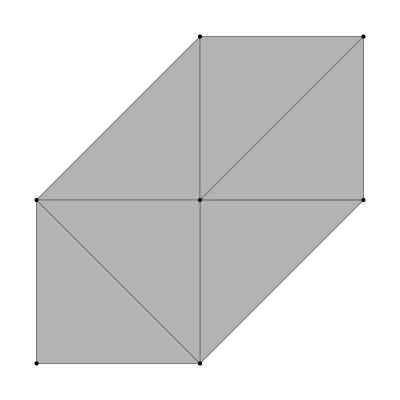
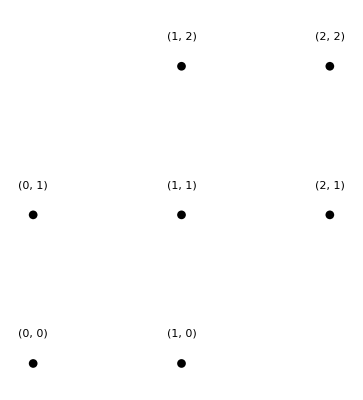
{RemoveAntz→{X_{4,8},X_{6,2}},NewToricTiang→-Graphics-,NewToricDiag→-Graphics-,DimerArea→6}

```mathematica
DimerDemo[]
```